# NP in the tails in p p → μ μ

## Theory

### Feyn Calc computation

```mathematica
$LoadFeynArts=False;
<<HighEnergyPhysics`FeynCalc`
```

Loading FeynCalc from /Users/admirgreljo/Library/Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Conversion factor: 1GeV^-2 = 0.3894 10^9 pb

```mathematica
KF=0.3894 10^9;
```

```mathematica
pcm[s_,m1_,m2_]:=(√s)/2 √(1+((m1^2-m2^2)^2)/s^2-2(m1^2+m2^2)/s);
t0[s_,m1_,m2_,m3_,m4_]:=((m1^2+m4^2-m2^2-m3^2)^2)/(4s)-(pcm[s,m1,m2]-pcm[s,m3,m4])^2;
t1[s_,m1_,m2_,m3_,m4_]:=((m1^2+m4^2-m2^2-m3^2)^2)/(4s)-(pcm[s,m1,m2]+pcm[s,m3,m4])^2;
```

```mathematica
Kinematika[m1_,m2_,m3_,m4_,s_,t_,u_]:=(ClearScalarProducts;
ScalarProduct[p1,p1]=m1^2;
ScalarProduct[p2,p2]=m2^2;
ScalarProduct[p3,p3]=m3^2;
ScalarProduct[p4,p4]=m4^2;
ScalarProduct[p1,p2]=(s-m1^2-m2^2)/2;
ScalarProduct[p1,p3]=(m1^2+m3^2-t)/2;
ScalarProduct[p1,p4]=(m1^2+m4^2-u)/2;
ScalarProduct[p2,p3]=(m2^2+m3^2-u)/2;
ScalarProduct[p2,p4]=(m2^2+m4^2-t)/2;
ScalarProduct[p3,p4]=(s-m3^2-m4^2)/2;)
```

```mathematica
{pcm[s,0,0],t0[s,0,0,0,0],t1[s,0,0,0,0]}
```

{(√s)/2,0,-s}

```mathematica
Kinematika[0,0,0,0,s,t,-s-t]
```

LL

```mathematica
1/4 TR[GS[p3].GA[α].GA[7].GS[p4].GA[β]] TR[GS[p2].GA[α].GA[7].GS[p1].GA[β]]//Contract//FullSimplify
```

(s+t)^2

RR

```mathematica
1/4 TR[GS[p3].GA[α].GA[6].GS[p4].GA[β]] TR[GS[p2].GA[α].GA[6].GS[p1].GA[β]]//Contract//FullSimplify
```

(s+t)^2

LR

```mathematica
1/4 TR[GS[p3].GA[α].GA[7].GS[p4].GA[β]] TR[GS[p2].GA[α].GA[6].GS[p1].GA[β]]//Contract//FullSimplify
```

t^2

RL

```mathematica
1/4 TR[GS[p3].GA[α].GA[6].GS[p4].GA[β]] TR[GS[p2].GA[α].GA[7].GS[p1].GA[β]]//Contract//FullSimplify
```

t^2

```mathematica
dσdtLL[s_,t_]:=1/(64π s pcm[s,0,0]^2)(s+t)^2/3
dσdtLR[s_,t_]:=1/(64π s pcm[s,0,0]^2)t^2/3
```

```mathematica
dσdtLL[s,t]
dσdtLR[s,t]
```

(s+t)^2/(48 π s^2)

t^2/(48 π s^2)

```mathematica
Integrate[dσdtLL[s,t],{t,t1[s,0,0,0,0],t0[s,0,0,0,0]},Assumptions->{{}}]
Integrate[dσdtLR[s,t],{t,t1[s,0,0,0,0],t0[s,0,0,0,0]},Assumptions->{{}}]
```

s/(144 π)

s/(144 π)

### Parton density

Read in p.d.f.

```mathematica
pdfpath="/home/arman/mmht2014code";
SetDirectory[pdfpath];
```

```mathematica
<<mstwpdf.m
```

Mathematica package for MSTW/MMHT PDFs
originally by Graeme Watt <Graeme.Watt(at)durham.ac.uk>.
For information on usage, see ?ReadPDFGrid and ?xf.
The update for MMHT2014 PDFs simply amounts to a redefinition 
of nhess in mstwpdf.m to reflect the increase in the number of
eigenvector sets. Note that 90% confidence level eigenvectors are 
not provided for MMHT2014 PDFs.

```mathematica
?xf
```

The function xf[ih,x,q,f] returns x times the parton distribution of flavour f corresponding to eigenvector set ih, where ih=0 is the central set, at a given momentum fraction x and scale q in GeV.  Note that ih and f must be integers, and x and q must be numeric quantities.  The PDG convention is used for the flavour f (apart from the gluon has f=0, not 21), that is, f = -6, -5, -4, -3, -2, -1, 0, 1, 2, 3, 4, 5, 6 corresponds to tbar, bbar, cbar, sbar, ubar, dbar, g, d, u, s, c, b, t.  The valence quark distributions can also be obtained directly with f = 7, 8, 9, 10, 11, 12 corresponding to dv, uv, sv, cv, bv, tv.  The photon distribution is obtained with f = 13.

```mathematica
prefix="/home/arman/mmht2014grids/mmht2014nnlo118/mmht2014nnlo118";
Timing[ReadPDFGrid[prefix,0]]
```

PDF grid read from /home/arman/mmht2014grids/mmht2014nnlo118/mmht2014nnlo118.00.dat

{11.2053,Null}

Definitions

```mathematica
dLbb[τ_,x_,μF_]:=1/(τ x)xf[0,x,μF,5] xf[0,τ/x,μF,-5];
Lbb[τ_,μF_]:=NIntegrate[dLbb[τ,x,μF],{x,τ,1},MaxRecursion->100];
dLuu[τ_,x_,μF_]:=1/(τ x)xf[0,x,μF,2] xf[0,τ/x,μF,-2];
Luu[τ_,μF_]:=NIntegrate[dLuu[τ,x,μF],{x,τ,1},MaxRecursion->100];
dLdd[τ_,x_,μF_]:=1/(τ x)xf[0,x,μF,1] xf[0,τ/x,μF,-1];
Ldd[τ_,μF_]:=NIntegrate[dLdd[τ,x,μF],{x,τ,1},MaxRecursion->100];
dLcc[τ_,x_,μF_]:=1/(τ x)xf[0,x,μF,4] xf[0,τ/x,μF,-4];
Lcc[τ_,μF_]:=NIntegrate[dLcc[τ,x,μF],{x,τ,1},MaxRecursion->100];
dLss[τ_,x_,μF_]:=1/(τ x)xf[0,x,μF,3] xf[0,τ/x,μF,-3];
Lss[τ_,μF_]:=NIntegrate[dLss[τ,x,μF],{x,τ,1},MaxRecursion->100];
```

```mathematica
RatioPDF[Mμμ_,μF_]:=Module[{lista},
lista={Luu[(Mμμ/13000)^2,μF],Ldd[(Mμμ/13000)^2,μF],Lss[(Mμμ/13000)^2,μF],Lcc[(Mμμ/13000)^2,μF],Lbb[(Mμμ/13000)^2,μF]};
lista/Sum[lista[[i]],{i,1,5}]
];
```

Variation with the factorization scale

```mathematica
RatioPDF[1000,500]
RatioPDF[1000,750]
RatioPDF[1000,1000]
RatioPDF[1000,1250]
RatioPDF[1000,1500]
RatioPDF[1000,2000]
```

{0.596935,0.351441,0.0320048,0.014109,0.00551051}

{0.597196,0.350285,0.032194,0.014472,0.00585252}

{0.597377,0.349519,0.0323132,0.0147098,0.00608071}

{0.59752,0.348948,0.032397,0.0148842,0.00625014}

{0.597636,0.348499,0.0324611,0.0150204,0.0063839}

{0.597818,0.347815,0.0325552,0.0152249,0.00658662}

```mathematica
RatioPDF[3000,3000/2]
RatioPDF[3000,3000]
RatioPDF[3000,3000*2]
```

{0.692223,0.29623,0.0068488,0.00356809,0.00113012}

{0.694411,0.29375,0.00692112,0.00369938,0.0012184}

{0.696411,0.291496,0.00697984,0.00381515,0.00129788}

Table

```mathematica
matricaRatioPDF=Table[RatioPDF[minv,minv],{minv,500,4100,50}];
```

$Aborted

```mathematica
Round[matricaRatioPDF,0.001]//MatrixForm
```

(0.552 | 0.345 | 0.06 | 0.03 | 0.013
0.558 | 0.346 | 0.056 | 0.027 | 0.012
0.564 | 0.347 | 0.052 | 0.025 | 0.011
0.57 | 0.348 | 0.049 | 0.024 | 0.01
0.575 | 0.348 | 0.046 | 0.022 | 0.009
0.579 | 0.349 | 0.043 | 0.02 | 0.009
0.583 | 0.349 | 0.041 | 0.019 | 0.008
0.587 | 0.349 | 0.038 | 0.018 | 0.007
0.591 | 0.349 | 0.036 | 0.017 | 0.007
0.594 | 0.349 | 0.034 | 0.016 | 0.006
0.597 | 0.35 | 0.032 | 0.015 | 0.006
0.6 | 0.349 | 0.031 | 0.014 | 0.006
0.603 | 0.349 | 0.029 | 0.013 | 0.005
0.606 | 0.349 | 0.028 | 0.012 | 0.005
0.608 | 0.349 | 0.026 | 0.012 | 0.005
0.611 | 0.349 | 0.025 | 0.011 | 0.004
0.613 | 0.348 | 0.024 | 0.011 | 0.004
0.615 | 0.348 | 0.023 | 0.01 | 0.004
0.618 | 0.347 | 0.022 | 0.01 | 0.004
0.62 | 0.347 | 0.021 | 0.009 | 0.004
0.622 | 0.346 | 0.02 | 0.009 | 0.003
0.624 | 0.345 | 0.019 | 0.008 | 0.003
0.626 | 0.344 | 0.018 | 0.008 | 0.003
0.628 | 0.344 | 0.018 | 0.008 | 0.003
0.63 | 0.343 | 0.017 | 0.007 | 0.003
0.632 | 0.342 | 0.016 | 0.007 | 0.003
0.634 | 0.341 | 0.016 | 0.007 | 0.003
0.637 | 0.339 | 0.015 | 0.007 | 0.003
0.639 | 0.338 | 0.014 | 0.006 | 0.002
0.641 | 0.337 | 0.014 | 0.006 | 0.002
0.643 | 0.335 | 0.013 | 0.006 | 0.002
0.645 | 0.334 | 0.013 | 0.006 | 0.002
0.648 | 0.332 | 0.012 | 0.006 | 0.002
0.65 | 0.331 | 0.012 | 0.005 | 0.002
0.652 | 0.329 | 0.012 | 0.005 | 0.002
0.655 | 0.327 | 0.011 | 0.005 | 0.002
0.657 | 0.325 | 0.011 | 0.005 | 0.002
0.659 | 0.324 | 0.01 | 0.005 | 0.002
0.662 | 0.322 | 0.01 | 0.005 | 0.002
0.664 | 0.32 | 0.01 | 0.005 | 0.002
0.667 | 0.318 | 0.009 | 0.005 | 0.002
0.67 | 0.315 | 0.009 | 0.004 | 0.002
0.672 | 0.313 | 0.009 | 0.004 | 0.001
0.675 | 0.311 | 0.009 | 0.004 | 0.001
0.678 | 0.309 | 0.008 | 0.004 | 0.001
0.68 | 0.306 | 0.008 | 0.004 | 0.001
0.683 | 0.304 | 0.008 | 0.004 | 0.001
0.686 | 0.301 | 0.008 | 0.004 | 0.001
0.689 | 0.299 | 0.007 | 0.004 | 0.001
0.692 | 0.296 | 0.007 | 0.004 | 0.001
0.694 | 0.294 | 0.007 | 0.004 | 0.001
0.697 | 0.291 | 0.007 | 0.004 | 0.001
0.7 | 0.289 | 0.007 | 0.004 | 0.001
0.703 | 0.286 | 0.006 | 0.004 | 0.001
0.706 | 0.283 | 0.006 | 0.003 | 0.001
0.709 | 0.281 | 0.006 | 0.003 | 0.001
0.712 | 0.278 | 0.006 | 0.003 | 0.001
0.715 | 0.275 | 0.006 | 0.003 | 0.001
0.718 | 0.272 | 0.006 | 0.003 | 0.001
0.721 | 0.27 | 0.005 | 0.003 | 0.001
0.724 | 0.267 | 0.005 | 0.003 | 0.001
0.726 | 0.264 | 0.005 | 0.003 | 0.001
0.729 | 0.262 | 0.005 | 0.003 | 0.001
0.732 | 0.259 | 0.005 | 0.003 | 0.001
0.735 | 0.256 | 0.005 | 0.003 | 0.001
0.738 | 0.253 | 0.005 | 0.003 | 0.001
0.741 | 0.251 | 0.005 | 0.003 | 0.001
0.743 | 0.248 | 0.004 | 0.003 | 0.001
0.746 | 0.246 | 0.004 | 0.003 | 0.001
0.749 | 0.243 | 0.004 | 0.003 | 0.001
0.751 | 0.24 | 0.004 | 0.003 | 0.001
0.754 | 0.238 | 0.004 | 0.003 | 0.001
0.757 | 0.235 | 0.004 | 0.003 | 0.001)

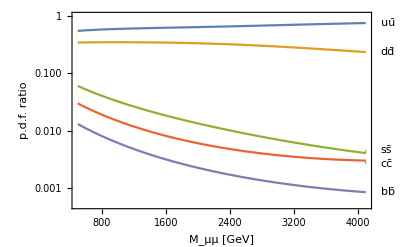

```mathematica
ListLogPlot[{Table[{450+50i,matricaRatioPDF[[i,1]]},{i,1,Length[matricaRatioPDF]}],Table[{450+50i,matricaRatioPDF[[i,2]]},{i,1,Length[matricaRatioPDF]}],Table[{450+50i,matricaRatioPDF[[i,3]]},{i,1,Length[matricaRatioPDF]}],Table[{450+50i,matricaRatioPDF[[i,4]]},{i,1,Length[matricaRatioPDF]}],Table[{450+50i,matricaRatioPDF[[i,5]]},{i,1,Length[matricaRatioPDF]}]},PlotLabels->{"uū","dd̄","ss̄","cc̄","bb̄"},Joined->True,PlotRange->{{500,4100},{0.5 10^-3,1}},Frame->True,GridLines->Automatic,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{{Style["p.d.f. ratio", FontSize->15,FontFamily->"Times New Roman",Italic,Black],""},{Style["M_μμ [GeV]", FontSize->15,FontFamily->"Times New Roman",Italic,Black],Style["mmht2014nnlo118", FontSize->13,FontFamily->"Times New Roman",Bold,Italic,Black]}},ImageSize->400]
```

```mathematica
fPDFuu=Interpolation[Table[{450+50i,matricaRatioPDF[[i,1]]},{i,1,Length[matricaRatioPDF]}]];
fPDFdd=Interpolation[Table[{450+50i,matricaRatioPDF[[i,2]]},{i,1,Length[matricaRatioPDF]}]];
fPDFss=Interpolation[Table[{450+50i,matricaRatioPDF[[i,3]]},{i,1,Length[matricaRatioPDF]}]];
fPDFcc=Interpolation[Table[{450+50i,matricaRatioPDF[[i,4]]},{i,1,Length[matricaRatioPDF]}]];
fPDFbb=Interpolation[Table[{450+50i,matricaRatioPDF[[i,5]]},{i,1,Length[matricaRatioPDF]}]];
```

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

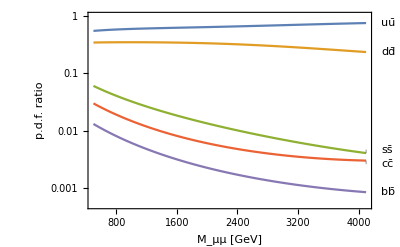

```mathematica
LogPlot[{fPDFuu[m],fPDFdd[m],fPDFss[m],fPDFcc[m],fPDFbb[m]},{m,500,4100},PlotLabels->{"uū","dd̄","ss̄","cc̄","bb̄"},PlotRange->{{500,4100},{0.5 10^-3,1}},Frame->True,GridLines->Automatic,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{{Style["p.d.f. ratio", FontSize->15,FontFamily->"Times New Roman",Italic,Black],""},{Style["M_μμ [GeV]", FontSize->15,FontFamily->"Times New Roman",Italic,Black],Style["mmht2014nnlo118", FontSize->13,FontFamily->"Times New Roman",Bold,Italic,Black]}},ImageSize->400]
```

### Form Factor

Standard Model inputs

```mathematica
mZNum=91.1876;
vEW=246.22;
sWNum=0.472643;
eNum=0.312183;
cWNum=√(1-sWNum^2);
gNum=eNum/sWNum;gYNum=eNum/cWNum;
gZeL=gNum/cWNum(T3f-Qf sWNum^2)/.{T3f->-1/2,Qf->-1}
gZeR=gNum/cWNum(T3f-Qf sWNum^2)/.{T3f->0,Qf->-1}
gZuL=gNum/cWNum(T3f-Qf sWNum^2)/.{T3f->1/2,Qf->2/3}
gZuR=gNum/cWNum(T3f-Qf sWNum^2)/.{T3f->0,Qf->2/3}
gZdL=gNum/cWNum(T3f-Qf sWNum^2)/.{T3f->-1/2,Qf->-1/3}
gZdR=gNum/cWNum(T3f-Qf sWNum^2)/.{T3f->0,Qf->-1/3}
```

-0.20732

0.167433

0.263131

-0.111622

-0.318942

0.055811

BLOCK WZPOLE

```mathematica
mZNum=91.1876;
vEW=246.22;
gZeL=(2 mZNum)/vEW *(-0.26963)
gZeR=(2 mZNum)/vEW *(0.2317)
gZuL=(2 mZNum)/vEW *(0.3467)
gZuR=(2 mZNum)/vEW *(-0.1547)
gZdL=(2 mZNum)/vEW *(-0.4243)
gZdR=(2 mZNum)/vEW *(0.07735)
```

-0.199715

0.17162

0.256801

-0.114586

-0.314279

0.0572932

Form factor definition

```mathematica
Clear[FF];
```

```mathematica
FF[Qq_,gZq_,gZl_,Cql_,s_]:=(-eNum^2 Qq)/s+(gZq gZl)/(s-mZNum^2)+Cql;
```

### Main formula

Definicije

```mathematica
Clear[upSUMFF, charmSUMFF, strangeSUMFF, downSUMFF, bottomSUMFF];
```

```mathematica
upSUMFF[CuLμL_,CuLμR_,CuRμL_,CuRμR_,Mμμ_]:=(Abs[FF[2/3,gZuL,gZeL,CuLμL,Mμμ^2]]^2+Abs[FF[2/3,gZuL,gZeR,CuLμR,Mμμ^2]]^2+Abs[FF[2/3,gZuR,gZeL,CuRμL,Mμμ^2]]^2+Abs[FF[2/3,gZuR,gZeR,CuRμR,Mμμ^2]]^2);
charmSUMFF[CcLμL_,CcLμR_,CcRμL_,CcRμR_,Mμμ_]:=(Abs[FF[2/3,gZuL,gZeL,CcLμL,Mμμ^2]]^2+Abs[FF[2/3,gZuL,gZeR,CcLμR,Mμμ^2]]^2+Abs[FF[2/3,gZuR,gZeL,CcRμL,Mμμ^2]]^2+Abs[FF[2/3,gZuR,gZeR,CcRμR,Mμμ^2]]^2);
downSUMFF[CdLμL_,CdLμR_,CdRμL_,CdRμR_,Mμμ_]:=(Abs[FF[-1/3,gZdL,gZeL,CdLμL,Mμμ^2]]^2+Abs[FF[-1/3,gZdL,gZeR,CdLμR,Mμμ^2]]^2+Abs[FF[-1/3,gZdR,gZeL,CdRμL,Mμμ^2]]^2+Abs[FF[-1/3,gZdR,gZeR,CdRμR,Mμμ^2]]^2);
strangeSUMFF[CsLμL_,CsLμR_,CsRμL_,CsRμR_,Mμμ_]:=(Abs[FF[-1/3,gZdL,gZeL,CsLμL,Mμμ^2]]^2+Abs[FF[-1/3,gZdL,gZeR,CsLμR,Mμμ^2]]^2+Abs[FF[-1/3,gZdR,gZeL,CsRμL,Mμμ^2]]^2+Abs[FF[-1/3,gZdR,gZeR,CsRμR,Mμμ^2]]^2);
bottomSUMFF[CbLμL_,CbLμR_,CbRμL_,CbRμR_,Mμμ_]:=(Abs[FF[-1/3,gZdL,gZeL,CbLμL,Mμμ^2]]^2+Abs[FF[-1/3,gZdL,gZeR,CbLμR,Mμμ^2]]^2+Abs[FF[-1/3,gZdR,gZeL,CbRμL,Mμμ^2]]^2+Abs[FF[-1/3,gZdR,gZeR,CbRμR,Mμμ^2]]^2);
```

Definicije

```mathematica
Clear[absTOT, relNevs];
```

```mathematica
absTOT[CuLμL_,CuLμR_,CuRμL_,CuRμR_,CdLμL_,CdLμR_,CdRμL_,CdRμR_,CsLμL_,CsLμR_,CsRμL_,CsRμR_,CcLμL_,CcLμR_,CcRμL_,CcRμR_,CbLμL_,CbLμR_,CbRμL_,CbRμR_,Mμμ_]:=fPDFuu[Mμμ] upSUMFF[CuLμL,CuLμR,CuRμL,CuRμR,Mμμ]+fPDFdd[Mμμ] downSUMFF[CdLμL,CdLμR,CdRμL,CdRμR,Mμμ]+fPDFss[Mμμ] strangeSUMFF[CsLμL,CsLμR,CsRμL,CsRμR,Mμμ]+fPDFcc[Mμμ] charmSUMFF[CcLμL,CcLμR,CcRμL,CcRμR,Mμμ]+fPDFbb[Mμμ] bottomSUMFF[CbLμL,CbLμR,CbRμL,CbRμR,Mμμ];
relNevs[CuLμL_,CuLμR_,CuRμL_,CuRμR_,CdLμL_,CdLμR_,CdRμL_,CdRμR_,CsLμL_,CsLμR_,CsRμL_,CsRμR_,CcLμL_,CcLμR_,CcRμL_,CcRμR_,CbLμL_,CbLμR_,CbRμL_,CbRμR_,Mμμ_]:=absTOT[CuLμL,CuLμR,CuRμL,CuRμR,CdLμL,CdLμR,CdRμL,CdRμR,CsLμL,CsLμR,CsRμL,CsRμR,CcLμL,CcLμR,CcRμL,CcRμR,CbLμL,CbLμR,CbRμL,CbRμR,Mμμ]/absTOT[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Mμμ];
```

### Ratio plot

Scenario 1. - MFV left-left

```mathematica
relONE[CL_,Mμμ_]:=relNevs[CL,CL,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Mμμ];
relTWO[CL_,Mμμ_]:=relNevs[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,CL,CL,0,0,Mμμ];
relTHREE[CL_,Mμμ_]:=relNevs[0,0,0,0,0,0,0,0,CL,CL,0,0,0,0,0,0,0,0,0,0,Mμμ];
```

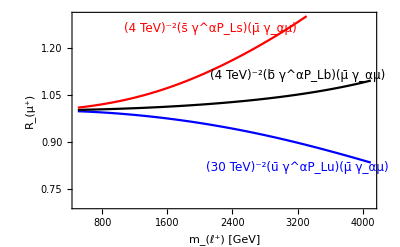

```mathematica
Show[Plot[{relONE[1/(30000)^2,Mμμ],relTWO[1/(4000)^2,Mμμ],relTHREE[1/(4000)^2,Mμμ]},{Mμμ,500,4100},PlotStyle->{Blue,Black,Red},PlotRange->{0.7,1.3},Frame->True,(*GridLines->Automatic,*)FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{{Style["R_(μ^+)", FontSize->20,FontFamily->"Times New Roman",Italic,Black],""},{Style["m_(ℓ^+) [GeV]", FontSize->18,FontFamily->"Times New Roman",Black],Style["dσ (pp → μ^+μ^-) / dσ (pp → e^+e^-) , s_0 = (13 TeV)^2", FontSize->13,FontFamily->"Times New Roman",Bold,Black]}},ImageSize->400],Graphics[Text[Style["(4 TeV)^-2(b̄ γ^αP_Lb)(μ̄ γ_αμ)", FontSize->12,FontFamily->"Times New Roman",Black],{3200,1.11}]],Graphics[Text[Style["(30 TeV)^-2(ū γ^αP_Lu)(μ̄ γ_αμ)", FontSize->12,FontFamily->"Times New Roman",Blue],{3200,0.82}]],Graphics[Text[Style["(4 TeV)^-2(s̄ γ^αP_Ls)(μ̄ γ_αμ)", FontSize->12,FontFamily->"Times New Roman",Red],{2125,1.26}]]]
```

### MFV scenario

```mathematica
relNevsMFV[CL_,Mμμ_]:=relNevs[CL,CL,0,0,CL,CL,0,0,CL,CL,0,0,CL,CL,0,0,CL,CL,0,0,Mμμ];
```

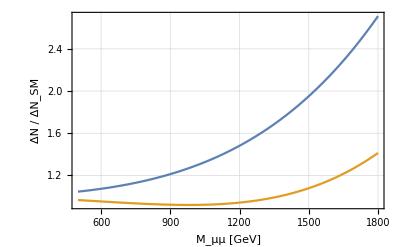

```mathematica
Plot[{relNevsMFV[-1/(20000/(√(4π)))^2,Mμμ],relNevsMFV[1/(20000/(√(4π)))^2,Mμμ]},{Mμμ,500,1800},Frame->True,GridLines->Automatic,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{{Style["ΔN / ΔN_SM", FontSize->15,FontFamily->"Times New Roman",Italic,Black],""},{Style["M_μμ [GeV]", FontSize->15,FontFamily->"Times New Roman",Italic,Black],Style["p p → μ μ @ 13 TeV", FontSize->13,FontFamily->"Times New Roman",Bold,Italic,Black]}},ImageSize->400]
```

```mathematica
Fit[Table[{coef 1/(20000/(√(4π)))^2,relNevsMFV[coef 1/(20000/(√(4π)))^2,2000]},{coef,-3,3,0.1}], {1,x,x^2}, x]
```

1.-2.60806×10^7 x+1.63295×10^15 x^2

```mathematica
1.0000000000000022-2.656201280042789*^7 x+1.6832412173259132*^15 x^2/.x->-1/(20000/(√(4π)))^2
```

3.49576

```mathematica
1.0000000000000022-2.656201280042789*^7 x/.x->-1/(20000/(√(4π)))^2
```

1.83447

### U(2) + predominantely third generation

```mathematica
relNevsU2[CLb_,Mμμ_]:=relNevs[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,CLb,CLb,0,0,Mμμ];
```

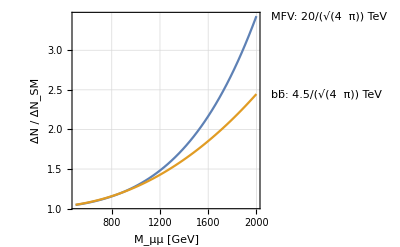

```mathematica
Plot[{relNevsMFV[-1/(20000/(√(4π)))^2,Mμμ],relNevsU2[1/(4500/(√(4π)))^2,Mμμ]},{Mμμ,500,2000},PlotLabels->{"MFV: 20/(√(4  π)) TeV","bb̄: 4.5/(√(4  π)) TeV"},Frame->True,GridLines->Automatic,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{{Style["ΔN / ΔN_SM", FontSize->15,FontFamily->"Times New Roman",Italic,Black],""},{Style["M_μμ [GeV]", FontSize->15,FontFamily->"Times New Roman",Italic,Black],Style["p p → μ μ @ 13 TeV", FontSize->13,FontFamily->"Times New Roman",Bold,Italic,Black]}},ImageSize->400]
```

## Experimental limits

### Data ATLAS

-Graphics-

Input data

```mathematica
NevsSIGNAL={1061.55427696188,940.681184613636,817.72955746092,680.732411324522,561.43713840981,527.501218435162,435.676910125236,401.816979208661,362.322113584553,297.771335242424,266.247202535631,223.531412430618,164.396105432764,151.160372911389,132.304512804005,113.236683227316,95.069377254294,88.0994524795649,63.0694222304742,59.3118803129221,52.425669257669,47.9199127009891,39.2368626613942,37.2320993209932,32.1395075673831,25.9662230126086,20.3381010712685,18.1645946317314,16.7725582381777,13.7277060725014,12.0079738497931,8.66371522039512,7.12310324858398,6.60967503962595,5.61544718309594,4.75308725007324,3.74174231837985,3.01040945707657,2.53118188084813,2.15212602547373,1.70991332919136,1.36669407936012,1.14323352304592,1.00540404974558,0.712798222054361,0.573480186931957,0.460413564368161,0.366364869429344,0.286906159806015,0.228969572604747,0.189180255410527,0.147944481762734,0.113070029278481,0.09122820472926,0.068536710205583,0.052512482492343,0.043932280019462,0.032207160223507,0.024243067054483,0.019776294861638}
NevsBCKG={500.017948246533,419.224177496676,364.429529099257,311.851469261524,271.972485726351,222.633868046836,194.163864749315,165.089918009056,130.530159247408,116.009405424806,93.4816691588383,78.4837900433919,64.0474491269686,54.4570336952858,46.453245616769,36.8417921225968,30.9310210631683,25.3208158600972,22.721389114067,17.906687631986,14.7058948549869,12.5038455481613,9.76192083729484,8.43253618873578,6.1988500807238,5.12308590374497,4.0126682597066,3.75113179458601,2.9567749511078,2.83487937712284,1.89494770180719,1.49363043126213,1.40537458320454,0.804734105549474,0.829862458776582,0.658158968026054,0.496259409894911,0.425968376144509,0.456304483710961,0.187422091308186,0.187271072783063,0.119021218785645,0.148403895842575,0.079007481503227,0.107662102852779,0.046952023097009,0.042663034052175,0.027636698348008,0.021642738303743,0.021216874195168,0.01370072876307,0.010934845716392,0.007105902323884,0.006216283008856,0.005170060078814,0.003234286563033,0.00287474027772,0.001983665227778,0.001618789022431,0.001193755328696}
(*Nexp=Round[Table[sigPbck[[i,2]],{i,1,Length[bck]}]]*)
(*Ovaj Nexp se i ne koristi!*) 
masa={470.265667969583,488.605496353547,508.665869374777,527.423435471319,546.872705704211,569.325319425153,590.319763818834,614.556156475869,637.218533527631,663.380419904274,687.843240829927,716.083594436583,742.489897988664,772.973845527744,801.478034370228,834.38382126329,868.640600653486,902.651244570303,933.885806310908,972.227777028882,1008.07965521943,1049.46775680595,1088.16793702185,1132.84417355481,1179.35465464034,1222.84454499385,1262.84674921776,1319.99512036053,1363.17535499902,1424.86395749051,1495.34878122122,1544.26525844416,1601.21159473259,1660.25788450954,1728.42206342946,1799.38481679445,1865.73894367075,1942.33943107744,2013.96515329297,2096.65127231603,2173.96739905009,2263.22263110622,2346.68124441233,2443.02748176773,2502.72367814098,2626.52780440376,2734.36352852105,2835.19593679969,2951.59881909417,3072.78078237935,3186.09266763815,3316.90209952137,3439.21620414964,3580.41797218291,3712.44948994332,3864.86922763872,4007.39017185114,4171.91910631645,4325.76282396621,4503.36298707885}(*dilepton invarijantna masa*)
```

```mathematica
DATA = {1561.57222520841,1359.90536211031,1182.15908656018,992.583880586046,833.409624136161,750.135086481998,629.840774874551,566.906897217717,492.852272831961,413.78074066723,359.728871694469,302.01520247401,228.443554559733,205.617406606674,178.757758420774,150.078475349913,126.000398317462,120.060151542732,92.5576971045281,89.8804574511872,75.2288484914482,52.9062700690122,54.9089256121359,34.3507224167364,23.4054518039667,34.1842278914222,29.4402911352611,19.1891298169233,23.852934792425,11.1179921521742,15.2869476756517,10.1573456516573,9.02818290539963,2.71144409948616,4.6678165882253,3.70201750440718,6.43436716696627,0.910112361311043,3.61189690312423,0.90570113747297,0.904971353438285,0.924404521391986,0.917841464318927,0.91412935350199,0,0,0.889042160662663,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
Length[DATA]
```

60

```mathematica
Length[NevsBCKG]
```

60

```mathematica
Length[NevsSIGNAL]
```

60

```mathematica
Length[masa]
```

60

Poisson statistics

```mathematica
pois[Δn_,μ_]:=PDF[PoissonDistribution[μ],Δn];
pois[Δn,μ]
```

Piecewise[{{(ⅇ^-μ μ^Δn)/(Δn!), Δn≥0}, {0, True}}]

### Cross check with ATLAS-CONF-2017-027

#### LEFT-LEFT

```mathematica
relLL[CLL_,Mμμ_]:=relNevs[CLL,0,0,0,CLL,0,0,0,CLL,0,0,0,CLL,0,0,0,CLL,0,0,0,Mμμ]
```

```mathematica
totχLL[CLL_]:=Sum[-2 Log[pois[Nexp[[bin]],NevsSIGNAL[[bin]]relLL[CLL,masa[[bin]]]+ NevsBCKG[[bin]]]],{bin,1,Length[bck]}];
```

```mathematica
rjmin=NMinimize[totχLL[1/((2π vEW)/eNum)^2 x],x]
```

{121.943,{x→0.0578825}}

Constructive

```mathematica
totχLL[-1/(26100/(√(4π)))^2]-rjmin[[1]]
```

7.33072

```mathematica
totχLL[-1/(30100/(√(4π)))^2]-rjmin[[1]]
```

4.05344

Destructive

```mathematica
totχLL[+1/(19600/(√(4π)))^2]-rjmin[[1]]
```

6.31512

```mathematica
totχLL[1/(21500/(√(4π)))^2]-rjmin[[1]]
```

4.05967

#### LEFT-RIGHT

```mathematica
relLR[CLR_,Mμμ_]:=relNevs[0,CLR,0,0,0,CLR,0,0,0,CLR,0,0,0,CLR,0,0,0,CLR,0,0,Mμμ]
```

```mathematica
totχLR[CLR_]:=Sum[-2 Log[pois[Nexp[[bin]],NevsSIGNAL[[bin]]relLR[CLR,masa[[bin]]]+ NevsBCKG[[bin]]]],{bin,1,Length[bck]}];
```

```mathematica
rjmin=NMinimize[totχLR[1/((2π vEW)/eNum)^2 x],x]
```

{121.991,{x→0.0306278}}

Constructive

```mathematica
totχLR[-1/(24400/(√(4π)))^2]-rjmin[[1]]
```

6.21971

```mathematica
totχLR[-1/(26800/(√(4π)))^2]-rjmin[[1]]
```

4.00834

Destructive

```mathematica
totχLR[+1/(21200/(√(4π)))^2]-rjmin[[1]]
```

5.17715

```mathematica
totχLR[1/(22200/(√(4π)))^2]-rjmin[[1]]
```

4.08268

#### RIGHT-LEFT

```mathematica
relRL[CLR_,Mμμ_]:=relNevs[0,0,CLR,0,0,0,CLR,0,0,0,CLR,0,0,0,CLR,0,0,0,CLR,0,Mμμ]
```

```mathematica
totχRL[CRL_]:=Sum[-2 Log[pois[Nexp[[bin]],NevsSIGNAL[[bin]]relRL[CRL,masa[[bin]]]+ NevsBCKG[[bin]]]],{bin,1,Length[bck]}];
```

```mathematica
rjmin=NMinimize[totχRL[1/((2π vEW)/eNum)^2 x],x]
```

{121.985,{x→0.0398826}}

Constructive

```mathematica
totχRL[-1/(24300/(√(4π)))^2]-rjmin[[1]]
```

6.0362

```mathematica
totχLR[-1/(26800/(√(4π)))^2]-rjmin[[1]]
```

4.01432

Destructive

```mathematica
totχLR[+1/(21000/(√(4π)))^2]-rjmin[[1]]
```

5.44593

```mathematica
totχLR[1/(22300/(√(4π)))^2]-rjmin[[1]]
```

3.99638

#### RIGHT-RIGHT

```mathematica
relRR[CLR_,Mμμ_]:=relNevs[0,0,0,CLR,0,0,0,CLR,0,0,0,CLR,0,0,0,CLR,0,0,0,CLR,Mμμ]
```

```mathematica
totχRR[CRL_]:=Sum[-2 Log[pois[Nexp[[bin]],NevsSIGNAL[[bin]]relRR[CRL,masa[[bin]]]+ NevsBCKG[[bin]]]],{bin,1,Length[bck]}];
```

```mathematica
rjmin=NMinimize[totχRR[1/((2π vEW)/eNum)^2 x],x]
```

{121.962,{x→0.0477759}}

Constructive

```mathematica
totχRR[-1/(24200/(√(4π)))^2]-rjmin[[1]]
```

9.77515

```mathematica
totχRR[-1/(29700/(√(4π)))^2]-rjmin[[1]]
```

4.0508

Destructive

```mathematica
totχRR[+1/(19700/(√(4π)))^2]-rjmin[[1]]
```

6.76249

```mathematica
totχRR[1/(22000/(√(4π)))^2]-rjmin[[1]]
```

4.03319

### LEFT-LEFT flavourfull limits - NOW - EXPECTED

```mathematica
relLLflavour[CLu_,CLd_,CLs_,CLc_,CLb_,Mμμ_]:=relNevs[CLu,0,0,0,CLd,0,0,0,CLs,0,0,0,CLc,0,0,0,CLb,0,0,0,Mμμ]
```

```mathematica
totχLLflavour[CLu_,CLd_,CLs_,CLc_,CLb_]:=Sum[-2 Log[pois[Nexp[[bin]],NevsSIGNAL[[bin]]relLLflavour[CLu,CLd,CLs,CLc,CLb,masa[[bin]]]+ NevsBCKG[[bin]]]],{bin,1,Length[bck]}];
```

```mathematica
rjmin=NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 x,0,0,0,0],x]
rjmin=NMinimize[totχLLflavour[0,1/(20000/(√(4π)))^2 x,0,0,0],x]
rjmin=NMinimize[totχLLflavour[0,0,1/(20000/(√(4π)))^2 x,0,0],x]
rjmin=NMinimize[totχLLflavour[0,0,0,1/(20000/(√(4π)))^2 x,0],x]
rjmin=NMinimize[totχLLflavour[0,0,0,0,1/(20000/(√(4π)))^2 x],x]
```

{121.956,{x→0.0395604}}

{121.984,{x→-0.0501304}}

{122.002,{x→-0.0618713}}

{122.002,{x→0.125829}}

{122.002,{x→-0.138726}}

```mathematica
30./√(4π)
```

8.46284

ALL quark flavours

```mathematica
{totχLLflavour[1/(8600)^2,0,0,0,0]-rjmin[[1]],totχLLflavour[-1/(10000)^2,0,0,0,0]-rjmin[[1]]}
{totχLLflavour[0,1/(7110)^2,0,0,0]-rjmin[[1]],totχLLflavour[0,-1/(5760)^2,0,0,0]-rjmin[[1]]}
{totχLLflavour[0,0,1/(2620)^2,0,0]-rjmin[[1]],totχLLflavour[0,0,-1/(2060)^2,0,0]-rjmin[[1]]}
{totχLLflavour[0,0,0,1/(1724)^2,0]-rjmin[[1]],totχLLflavour[0,0,0,-1/(2110)^2,0]-rjmin[[1]]}
{totχLLflavour[0,0,0,0,1/(1553)^2]-rjmin[[1]],totχLLflavour[0,0,0,0,-1/(1366)^2]-rjmin[[1]]}
```

{4.05361,4.06925}

{4.05958,4.05237}

{4.01405,4.06092}

{4.05449,4.06554}

{4.04931,4.05396}

```mathematica
{-vEW^2/(10000)^2,vEW^2/(8600)^2}
{-vEW^2/(5760)^2,vEW^2/(7110)^2}
{-vEW^2/(2060)^2,vEW^2/(2620)^2}
{-vEW^2/(2110)^2,vEW^2/(1724)^2}
{-vEW^2/(1366)^2,vEW^2/(1553)^2}
```

{-0.000606243,0.00081969}

{-0.00182727,0.00119924}

{-0.0142861,0.0088317}

{-0.013617,0.0203973}

{-0.0324897,0.0251364}

```mathematica
rjmin=NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 x,1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{x,y,z,w,v},Method->"DifferentialEvolution"]
```

{121.901,{x→0.110183,y→0.013697,z→1.03878,w→-0.497906,v→0.760424}}

UP

```mathematica
NMinimize[totχLLflavour[1/(5450)^2,1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

4.0883

```mathematica
NMinimize[totχLLflavour[-1/(8100)^2,1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

4.01296

DOWN

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,1/(5300)^2,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

4.045

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,-1/(4580)^2,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

4.00581

STRANGE

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(1890)^2,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

3.9942

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,-1/(1980)^2,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

4.02329

CHARM

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(1640)^2,1/(20000/(√(4π)))^2 v],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

3.95832

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,-1/(1575)^2,1/(20000/(√(4π)))^2 v],{y,z,w,v}][[1]]-rjmin[[1]]
```

3.9682

Bottom

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v,1/(1195)^2],{y,z,w,v}][[1]]-rjmin[[1]]
```

3.96864

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v,-1/(1220)^2],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

3.92794

```mathematica
{-vEW^2/(8100)^2,vEW^2/(5450)^2}
{-vEW^2/(4580)^2,vEW^2/(5300)^2}
{-vEW^2/(1980)^2,vEW^2/(1890)^2}
{-vEW^2/(1575)^2,vEW^2/(1640)^2}
{-vEW^2/(1220)^2,vEW^2/(1195)^2}
```

{-0.00092401,0.00204105}

{-0.00289012,0.00215822}

{-0.0154638,0.0169716}

{-0.0244391,0.0225403}

{-0.0407312,0.0424532}

### LEFT-LEFT flavourfull limits - 3000 fb^-1

```mathematica
relLLflavour[CLu_,CLd_,CLs_,CLc_,CLb_,Mμμ_]:=relNevs[CLu,0,0,0,CLd,0,0,0,CLs,0,0,0,CLc,0,0,0,CLb,0,0,0,Mμμ]
```

```mathematica
NexpFUTURE=Round[83.1 (NevsSIGNAL+NevsBCKG)]
```

{42461,33621,25276,20540,15847,11914,8957,6910,5332,4333,3257,2513,1794,1349,1040,669,490,388,270,178,138,93,65,45,31,21,14,9,6,4,3,2}

```mathematica
totχLLflavou3000[CLu_,CLd_,CLs_,CLc_,CLb_]:=Sum[-2 Log[pois[NexpFUTURE[[bin]],83.1 NevsSIGNAL[[bin]]relLLflavour[CLu,CLd,CLs,CLc,CLb,masa[[bin]]]+ 83.1 NevsBCKG[[bin]]]],{bin,1,Length[bck]}];
```

```mathematica
rjmin=NMinimize[totχLLflavou3000[1/(20000/(√(4π)))^2 x,0,0,0,0],x]
rjmin=NMinimize[totχLLflavou3000[0,1/(20000/(√(4π)))^2 x,0,0,0],x]
rjmin=NMinimize[totχLLflavou3000[0,0,1/(20000/(√(4π)))^2 x,0,0],x]
rjmin=NMinimize[totχLLflavou3000[0,0,0,1/(20000/(√(4π)))^2 x,0],x]
rjmin=NMinimize[totχLLflavou3000[0,0,0,0,1/(20000/(√(4π)))^2 x],x]
```

{255.067,{x→-0.000203157}}

{255.067,{x→-0.0000429646}}

{255.067,{x→-0.00111985}}

{255.067,{x→0.000272395}}

{255.067,{x→-0.00204807}}

ALL quark flavours

```mathematica
{totχLLflavou3000[1/(28200)^2,0,0,0,0]-rjmin[[1]],totχLLflavou3000[-1/(28000)^2,0,0,0,0]-rjmin[[1]]}
{totχLLflavou3000[0,1/(19150)^2,0,0,0]-rjmin[[1]],totχLLflavou3000[0,-1/(18800)^2,0,0,0]-rjmin[[1]]}
{totχLLflavou3000[0,0,1/(6180)^2,0,0]-rjmin[[1]],totχLLflavou3000[0,0,-1/(5500)^2,0,0]-rjmin[[1]]}
{totχLLflavou3000[0,0,0,1/(4034)^2,0]-rjmin[[1]],totχLLflavou3000[0,0,0,-1/(4760)^2,0]-rjmin[[1]]}
{totχLLflavou3000[0,0,0,0,1/(3138)^2]-rjmin[[1]],totχLLflavou3000[0,0,0,0,-1/(2378)^2]-rjmin[[1]]}
```

{3.95554,4.10175}

{4.06396,3.92522}

{4.0463,3.98398}

{4.04646,4.04142}

{4.03343,4.07825}

```mathematica
{-vEW^2/(28000)^2,vEW^2/(28200)^2}
{-vEW^2/(18800)^2,vEW^2/(19150)^2}
{-vEW^2/(5500)^2,vEW^2/(6180)^2}
{-vEW^2/(4760)^2,vEW^2/(4034)^2}
{-vEW^2/(2378)^2,vEW^2/(3138)^2}
```

{-0.0000773269,0.000076234}

{-0.000171526,0.000165314}

{-0.00200411,0.00158734}

{-0.00267567,0.00372542}

{-0.0107207,0.0061566}

```mathematica
rjmin=NMinimize[totχLLflavou3000[1/(20000/(√(4π)))^2 x,1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{x,y,z,w,v},Method->"DifferentialEvolution"]
```

{255.047,{x→0.111534,y→0.08718,z→1.83045,w→1.77109,v→-0.957356}}

UP

```mathematica
NMinimize[totχLLflavou3000[1/(9000)^2,1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v}(*,Method->"DifferentialEvolution"*)][[1]]-rjmin[[1]]
```

3.98408

```mathematica
NMinimize[totχLLflavou3000[-1/(15500)^2,1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v}(*,Method->"DifferentialEvolution"*)][[1]]-rjmin[[1]]
```

4.06681

DOWN

```mathematica
NMinimize[totχLLflavou3000[1/(20000/(√(4π)))^2 y,1/(8150)^2,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v}(*,Method->"DifferentialEvolution"*)][[1]]-rjmin[[1]]
```

4.06845

```mathematica
NMinimize[totχLLflavou3000[1/(20000/(√(4π)))^2 y,-1/(7840)^2,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

3.93977

STRANGE

```mathematica
NMinimize[totχLLflavou3000[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(2535)^2,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v}(*,Method->"DifferentialEvolution"*)][[1]]-rjmin[[1]]
```

4.05567

```mathematica
NMinimize[totχLLflavou3000[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,-1/(3505)^2,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v}(*,Method->"DifferentialEvolution"*)][[1]]-rjmin[[1]]
```

4.00731

CHARM

```mathematica
NMinimize[totχLLflavou3000[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(2720)^2,1/(20000/(√(4π)))^2 v],{y,z,w,v}(*,Method->"DifferentialEvolution"*)][[1]]-rjmin[[1]]
```

4.04257

```mathematica
NMinimize[totχLLflavou3000[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,-1/(2275)^2,1/(20000/(√(4π)))^2 v],{y,z,w,v}(*,Method->"DifferentialEvolution"*)][[1]]-rjmin[[1]]
```

4.01341

BOTTOM

```mathematica
NMinimize[totχLLflavou3000[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v,1/(1645)^2],{y,z,w,v}(*,Method->"DifferentialEvolution"*)][[1]]-rjmin[[1]]
```

4.08334

```mathematica
NMinimize[totχLLflavou3000[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v,-1/(1875)^2],{y,z,w,v}(*,Method->"DifferentialEvolution"*)][[1]]-rjmin[[1]]
```

3.97669

### LEFT-LEFT flavourfull limits - NOW - OBSERVED

```mathematica
relLLflavour[CLu_,CLd_,CLs_,CLc_,CLb_,Mμμ_]:=relNevs[CLu,0,0,0,CLd,0,0,0,CLs,0,0,0,CLc,0,0,0,CLb,0,0,0,Mμμ]
```

```mathematica
totχLLflavour[CLu_,CLd_,CLs_,CLc_,CLb_]:=Sum[-2 Log[pois[DATA[[bin]],NevsSIGNAL[[bin]]relLLflavour[CLu,CLd,CLs,CLc,CLb,masa[[bin]]]+ NevsBCKG[[bin]]]],{bin,1,Length[bck]}];
```

```mathematica
rjminU=NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 x,0,0,0,0],x,Method->"DifferentialEvolution"]
rjminD=NMinimize[totχLLflavour[0,1/(20000/(√(4π)))^2 x,0,0,0],x,Method->"DifferentialEvolution"]
rjminS=NMinimize[totχLLflavour[0,0,1/(20000/(√(4π)))^2 x,0,0],x,Method->"DifferentialEvolution"]
rjminC=NMinimize[totχLLflavour[0,0,0,1/(20000/(√(4π)))^2 x,0],x,Method->"DifferentialEvolution"]
rjminB=NMinimize[totχLLflavour[0,0,0,0,1/(20000/(√(4π)))^2 x],x,Method->"DifferentialEvolution"]
```

{130.818,{x→0.113931}}

{131.018,{x→-0.151456}}

{131.197,{x→-0.127192}}

{131.198,{x→0.173182}}

{131.199,{x→-0.112748}}

ALL quark flavours

```mathematica
{totχLLflavour[1/(10000)^2,0,0,0,0]-rjminU[[1]],totχLLflavour[-1/(10000)^2,0,0,0,0]-rjminU[[1]]}
{totχLLflavour[0,1/(7110)^2,0,0,0]-rjminD[[1]],totχLLflavour[0,-1/(5760)^2,0,0,0]-rjminD[[1]]}
{totχLLflavour[0,0,1/(2620)^2,0,0]-rjminS[[1]],totχLLflavour[0,0,-1/(2060)^2,0,0]-rjminS[[1]]}
{totχLLflavour[0,0,0,1/(1724)^2,0]-rjminC[[1]],totχLLflavour[0,0,0,-1/(2110)^2,0]-rjminC[[1]]}
{totχLLflavour[0,0,0,0,1/(1753)^2]-rjminB[[1]],totχLLflavour[0,0,0,0,-1/(1366)^2]-rjminB[[1]]}
```

{1.16104,5.75378}

{5.54712,4.07257}

{4.93538,6.08882}

{6.05994,5.071}

{2.79752,5.90773}

```mathematica
skale={{(7000/x)/.NMinimize[{(totχLLflavour[-x^2/(7000)^2,0,0,0,0]-rjminU[[1]]-4)^2,x>0},{x}][[2]],(7000/x)/.NMinimize[{(totχLLflavour[x^2/(7000)^2,0,0,0,0]-rjminU[[1]]-4)^2,x>0},{x}][[2]]},{(7000/x)/.NMinimize[{(totχLLflavour[0,-x^2/(7000)^2,0,0,0]-rjminD[[1]]-4)^2,x>0},{x}][[2]],(7000/x)/.NMinimize[{(totχLLflavour[0,x^2/(7000)^2,0,0,0]-rjminD[[1]]-4)^2,x>0},{x}][[2]]},{(7000/x)/.NMinimize[{(totχLLflavour[0,0,-x^2/(7000)^2,0,0]-rjminS[[1]]-4)^2,x>0},{x}][[2]],(7000/x)/.NMinimize[{(totχLLflavour[0,0,x^2/(7000)^2,0,0]-rjminS[[1]]-4)^2,x>0},{x}][[2]]},{(7000/x)/.NMinimize[{(totχLLflavour[0,0,0,-x^2/(7000)^2,0]-rjminC[[1]]-4)^2,x>0},{x}][[2]],(7000/x)/.NMinimize[{(totχLLflavour[0,0,0,x^2/(7000)^2,0]-rjminC[[1]]-4)^2,x>0},{x}][[2]]},{(7000/x)/.NMinimize[(totχLLflavour[0,0,0,0,-x^2/(7000)^2]-rjminB[[1]]-4)^2,{x}][[2]],(7000/x)/.NMinimize[(totχLLflavour[0,0,0,0,x^2/(7000)^2]-rjminB[[1]]-4)^2,{x}][[2]]}}
```

{{11326.,7974.23},{5784.2,7828.87},{2253.88,2737.24},{2216.41,1881.87},{1469.59,1633.56}}

```mathematica
{totχLLflavour[-1/(skale[[1,1]])^2,0,0,0,0]-rjminU[[1]],totχLLflavour[1/(skale[[1,2]])^2,0,0,0,0]-rjminU[[1]]}
{totχLLflavour[0,-1/(skale[[2,1]])^2,0,0,0]-rjminD[[1]],totχLLflavour[0,1/(skale[[2,2]])^2,0,0,0]-rjminD[[1]]}
{totχLLflavour[0,0,-1/(skale[[3,1]])^2,0,0]-rjminS[[1]],totχLLflavour[0,0,1/(skale[[3,2]])^2,0,0]-rjminS[[1]]}
{totχLLflavour[0,0,0,-1/(skale[[4,1]])^2,0]-rjminC[[1]],totχLLflavour[0,0,0,1/(skale[[4,2]])^2,0]-rjminC[[1]]}
{totχLLflavour[0,0,0,0,-1/(skale[[5,1]])^2]-rjminB[[1]],totχLLflavour[0,0,0,0,1/(skale[[5,2]])^2]-rjminB[[1]]}
```

{4.,4.}

{4.,4.}

{4.,4.}

«2 more identical outputs»

```mathematica
skale
```

{{11326.,7974.23},{5784.2,7828.87},{2253.88,2737.24},{2216.41,1881.87},{1469.59,1633.56}}

```mathematica
ScientificForm[Table[{-(vEW/skale[[i,1]])^2,(vEW/skale[[i,2]])^2},{i,1,5}]//MatrixForm,3]
```

(-4.73×10^-4 | 9.53×10^-4
-1.81×10^-3 | 9.89×10^-4
-1.19×10^-2 | 8.09×10^-3
-1.23×10^-2 | 1.71×10^-2
-2.81×10^-2 | 2.27×10^-2)

```mathematica
rjmin=NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 x,1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{x,y,z,w,v},Method->"DifferentialEvolution"]
```

{130.573,{x→0.191366,y→-0.075398,z→1.35578,w→-1.26866,v→1.6568}}

UP

```mathematica
NMinimize[totχLLflavour[1/(5950)^2,1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

3.98697

```mathematica
NMinimize[totχLLflavour[-1/(9400)^2,1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

4.02997

DOWN

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,1/(5950)^2,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

4.0076

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,-1/(5080)^2,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

4.05273

STRANGE

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(2030)^2,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

3.99686

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,-1/(2220)^2,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

4.04158

CHARM

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(1840)^2,1/(20000/(√(4π)))^2 v],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

3.92413

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,-1/(1705)^2,1/(20000/(√(4π)))^2 v],{y,z,w,v}][[1]]-rjmin[[1]]
```

3.94203

Bottom

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v,1/(1290)^2],{y,z,w,v}][[1]]-rjmin[[1]]
```

3.9969

```mathematica
NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 y,1/(20000/(√(4π)))^2 z,1/(20000/(√(4π)))^2 w,1/(20000/(√(4π)))^2 v,-1/(1345)^2],{y,z,w,v},Method->"DifferentialEvolution"][[1]]-rjmin[[1]]
```

3.98496

### LEFT-VECTOR flavourfull limits - NOW-EXPECTED

```mathematica
relLLflavour[CLu_,CLd_,CLs_,CLc_,CLb_,Mμμ_]:=relNevs[CLu,CLu,0,0,CLd,CLd,0,0,CLs,CLs,0,0,CLc,CLc,0,0,CLb,CLb,0,0,Mμμ]
```

```mathematica
totχLLflavour[CLu_,CLd_,CLs_,CLc_,CLb_]:=Sum[-2 Log[pois[Nexp[[bin]],NevsSIGNAL[[bin]]relLLflavour[CLu,CLd,CLs,CLc,CLb,masa[[bin]]]+ NevsBCKG[[bin]]]],{bin,1,Length[bck]}];
```

```mathematica
rjmin=NMinimize[totχLLflavour[1/(20000/(√(4π)))^2 x,0,0,0,0],x]
```

{121.958,{x→0.0323785}}

```mathematica
totχLLflavour[0,0,0,0,0]
```

122.002

```mathematica
30./√(4π)
```

8.46284

ALL quark flavours (ovi su mi malo jaci)

```mathematica
{totχLLflavour[1/(8600)^2,0,0,0,0]-rjmin[[1]],totχLLflavour[-1/(10000)^2,0,0,0,0]-rjmin[[1]]}
{totχLLflavour[0,1/(7110)^2,0,0,0]-rjmin[[1]],totχLLflavour[0,-1/(5760)^2,0,0,0]-rjmin[[1]]}
{totχLLflavour[0,0,1/(2620)^2,0,0]-rjmin[[1]],totχLLflavour[0,0,-1/(2060)^2,0,0]-rjmin[[1]]}
{totχLLflavour[0,0,0,1/(1724)^2,0]-rjmin[[1]],totχLLflavour[0,0,0,-1/(2110)^2,0]-rjmin[[1]]}
{totχLLflavour[0,0,0,0,1/(1553)^2]-rjmin[[1]],totχLLflavour[0,0,0,0,-1/(1366)^2]-rjmin[[1]]}
```

{5.1687,5.90412}

{4.33738,3.56379}

{6.86682,14.0139}

{12.3202,9.13482}

{9.45819,14.8225}

### MFV scenario

```mathematica
3000/36.1
```

83.1025

```mathematica
totLhU2[CLb_]:=Sum[-2 Log[pois[Nexp[[bin]],NevsSIGNAL[[bin]]relNevsU2[CLb,masa[[bin]]]+ NevsBCKG[[bin]]]],{bin,1,Length[bck]}];
totLhU23000[CLb_]:=Sum[-2 Log[pois[83 Nexp[[bin]],83 NevsSIGNAL[[bin]]relNevsU2[CLb,masa[[bin]]]+83 NevsBCKG[[bin]]]],{bin,1,Length[bck]}];
```

```mathematica
rjmin=NMinimize[totLhU2[1/((2π vEW)/eNum)^2 x],x]
```

{122.002,{x→-0.0529547}}

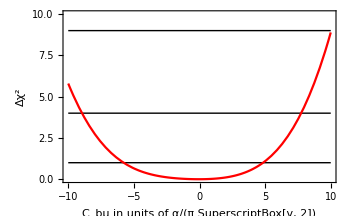

```mathematica
Plot[{1,4,9,totLhU2[1/((2π vEW)/eNum)^2 x]-rjmin[[1]]},{x,-10,10},PlotStyle->{{Thin,Black},{Thin,Black},{Thin,Black},Red},Frame->True,PlotRange->{0,10},FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{{Style["Δχ^2", FontSize->15,FontFamily->"Times New Roman",Italic,Black],""},{Style["C_bμ in units of α/(π SuperscriptBox[v, 2])", FontSize->15,FontFamily->"Times New Roman",Black],""}},ImageSize->350]
```

```mathematica
rjmin=NMinimize[totLhU23000[1/((2π vEW)/eNum)^2 x],x]
```

{448.477,{x→-0.0529548}}

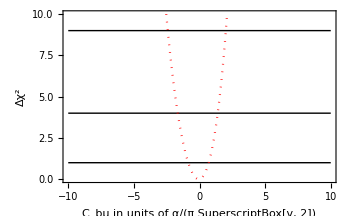

```mathematica
Plot[{1,4,9,totLhU23000[1/((2π vEW)/eNum)^2 x]-rjmin[[1]]},{x,-10,10},PlotStyle->{{Thin,Black},{Thin,Black},{Thin,Black},{Red,Dotted}},Frame->True,PlotRange->{0,10},FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{{Style["Δχ^2", FontSize->15,FontFamily->"Times New Roman",Italic,Black],""},{Style["C_bμ in units of α/(π SuperscriptBox[v, 2])", FontSize->15,FontFamily->"Times New Roman",Black],Style["U(2)_q + third generation only", FontSize->13,FontFamily->"Times New Roman",Bold,Italic,Black]}},ImageSize->350]
```

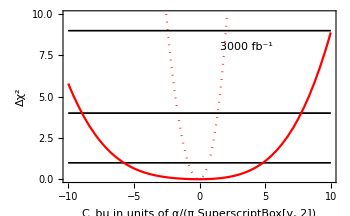

```mathematica
Show[-Graphics-,-Graphics-,Graphics[Text["3000 fb^-1",{3.6,8}]]]
```

```mathematica
totLhMFV[CL_]:=Sum[-2 Log[pois[Nexp[[bin]],NevsSIGNAL[[bin]]relNevsMFV[CL,masa[[bin]]]+NevsBCKG[[bin]]]],{bin,1,Length[bck]}]
totLhMFV300[CL_]:=Sum[-2 Log[pois[8 Nexp[[bin]],8 NevsSIGNAL[[bin]]relNevsMFV[CL,masa[[bin]]]+8 NevsBCKG[[bin]]]],{bin,1,Length[bck]}]
```

```mathematica
rjmin=NMinimize[totLhMFV[1/((2π vEW)/eNum)^2 x],x]
```

{121.955,{x→0.0338834}}

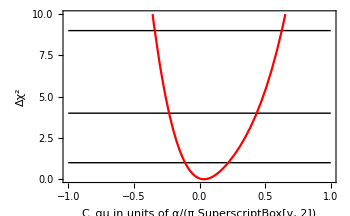

```mathematica
Plot[{1,4,9,totLhMFV[1/((2π vEW)/eNum)^2 x]-rjmin[[1]]},{x,-1,1},PlotStyle->{{Thin,Black},{Thin,Black},{Thin,Black},Red},Frame->True,PlotRange->{0,10},FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{{Style["Δχ^2", FontSize->15,FontFamily->"Times New Roman",Italic,Black],""},{Style["C_qμ in units of α/(π SuperscriptBox[v, 2])", FontSize->15,FontFamily->"Times New Roman",Black],""}},ImageSize->350]
```

```mathematica
rjmin=NMinimize[totLhMFV300[1/((2π vEW)/eNum)^2 x],x]
```

{189.685,{x→0.0338835}}

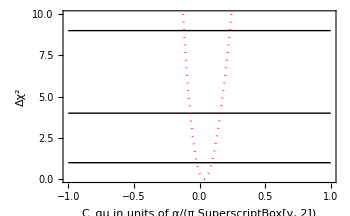

```mathematica
Plot[{1,4,9,totLhMFV300[1/((2π vEW)/eNum)^2 x]-rjmin[[1]]},{x,-1,1},PlotStyle->{{Thin,Black},{Thin,Black},{Thin,Black},{Red,Dotted}},Frame->True,PlotRange->{0,10},FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{{Style["Δχ^2", FontSize->15,FontFamily->"Times New Roman",Italic,Black],""},{Style["C_qμ in units of α/(π SuperscriptBox[v, 2])", FontSize->15,FontFamily->"Times New Roman",Black],Style["Minimal flavour violation", FontSize->13,FontFamily->"Times New Roman",Bold,Italic,Black]}},ImageSize->350]
```

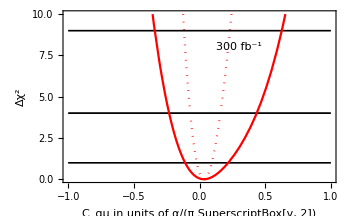

```mathematica
Show[-Graphics-,-Graphics-,Graphics[Text["300 fb^-1",{0.3,8}]]]
```

```mathematica
(2π vEW)/eNum
```

4955.57

## BIG TABLE - Muon

### NOW

```mathematica
Clear[totχALL];
```

```mathematica
totχALL[C1q1μL_,C3q1μL_,CuRμL_,CuRμR_,Cq1μR_,CdRμL_,CdRμR_,C1q2μL_,C3q2μL_,Cq2μR_,CsRμL_,CsRμR_,CcRμL_,CcRμR_,CbLμL_,CbLμR_,CbRμL_,CbRμR_]:=Sum[-2 Log[pois[DATA[[bin]],NevsSIGNAL[[bin]]relNevs[(C1q1μL-C3q1μL)/vEW^2,Cq1μR/vEW^2,CuRμL/vEW^2,CuRμR/vEW^2,(C1q1μL+C3q1μL)/vEW^2,Cq1μR/vEW^2,CdRμL/vEW^2,CdRμR/vEW^2,(C1q2μL+C3q2μL)/vEW^2,Cq2μR/vEW^2,CsRμL/vEW^2,CsRμR/vEW^2,(C1q2μL-C3q2μL)/vEW^2,Cq2μR/vEW^2,CcRμL/vEW^2,CcRμR/vEW^2,CbLμL/vEW^2,CbLμR/vEW^2,CbRμL/vEW^2,CbRμR/vEW^2,masa[[bin]]]+ NevsBCKG[[bin]]]],{bin,1,60}];
```

```mathematica
Clear[lista];
```

```mathematica
lista=Table[x KroneckerDelta[i,j],{i,18},{j,18}];
lista//MatrixForm
```

(x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x)

```mathematica
Clear[rjmin];
```

```mathematica
lista[[1]]
```

{x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
totχALL[lista[[1]]]
```

∞

```mathematica
Clear x;
```

```mathematica
rjmin=NMinimize[totχALL[lista[[1]]],x]
```

Infinity::indet: Indeterminate expression 0 ∞ encountered.

NMinimize::nnum: The function value ∞ is not a number at {x} = {-0.829053}.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NMinimize::nnum: The function value ∞ is not a number at {x} = {-0.829053}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

NMinimize[∞,x]

Muon present limits

{-6.49×10^-4,1.38×10^-3}

{-6.48×10^-4,3.42×10^-4}

{-9.19×10^-4,1.59×10^-3}

{-6.22×10^-4,1.27×10^-3}

{-8.89×10^-4,1.29×10^-3}

{-2.23×10^-3,1.75×10^-3}

{-2.32×10^-3,1.5×10^-3}

{-9.58×10^-3,8.1×10^-3}

{-9.19×10^-3,6.06×10^-3}

{-8.33×10^-3,9.39×10^-3}

{-1.14×10^-2,1.03×10^-2}

{-1.18×10^-2,9.68×10^-3}

{-1.45×10^-2,1.65×10^-2}

{-1.33×10^-2,1.71×10^-2}

{-2.81×10^-2,2.27×10^-2}

{-2.52×10^-2,2.64×10^-2}

{-2.64×10^-2,2.52×10^-2}

{-2.69×10^-2,2.45×10^-2}

### Projections

```mathematica
NexpFUTURE=Round[83.1 (NevsSIGNAL+NevsBCKG)]
```

{42461,33621,25276,20540,15847,11914,8957,6910,5332,4333,3257,2513,1794,1349,1040,669,490,388,270,178,138,93,65,45,31,21,14,9,6,4,3,2}

```mathematica
totχALL3000[{C1q1μL_,C3q1μL_,CuRμL_,CuRμR_,Cq1μR_,CdRμL_,CdRμR_,C1q2μL_,C3q2μL_,Cq2μR_,CsRμL_,CsRμR_,CcRμL_,CcRμR_,CbLμL_,CbLμR_,CbRμL_,CbRμR_}]:=Sum[-2 Log[pois[NexpFUTURE[[bin]],83.1 NevsSIGNAL[[bin]]relNevs[(C1q1μL-C3q1μL)/vEW^2,Cq1μR/vEW^2,CuRμL/vEW^2,CuRμR/vEW^2,(C1q1μL+C3q1μL)/vEW^2,Cq1μR/vEW^2,CdRμL/vEW^2,CdRμR/vEW^2,(C1q2μL+C3q2μL)/vEW^2,Cq2μR/vEW^2,CsRμL/vEW^2,CsRμR/vEW^2,(C1q2μL-C3q2μL)/vEW^2,Cq2μR/vEW^2,CcRμL/vEW^2,CcRμR/vEW^2,CbLμL/vEW^2,CbLμR/vEW^2,CbRμL/vEW^2,CbRμR/vEW^2,masa[[bin]]]+83.1  NevsBCKG[[bin]]]],{bin,1,Length[bck]}];
```

```mathematica
lista=Table[x KroneckerDelta[i,j],{i,18},{j,18}];
lista//MatrixForm
```

(x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x)

```mathematica
rjmin=NMinimize[totχALL3000[lista[[1]]],x]
```

{255.067,{x→-1.33005×10^-6}}

```mathematica
For[i=1;i≤18,i++,
Print[i]]

{x/.NMinimize[{(totχALL3000[lista[[1]]]-rjmin[[1]]-4)^2,x<0},{x}][[2]],x/.NMinimize[{(totχALL3000[lista[[1]]]-rjmin[[1]]-4)^2,x>0},{x}][[2]]}
```

{-0.000131352,0.000149832}

```mathematica
For[i=1,i≤18,i++,

rjmin=NMinimize[totχALL3000[lista[[i]]],x];

Print[ScientificForm[{x/.NMinimize[{(totχALL3000[lista[[i]]]-rjmin[[1]]-4)^2,x<0},{x}][[2]],x/.NMinimize[{(totχALL3000[lista[[i]]]-rjmin[[1]]-4)^2,x>0},{x}][[2]]},3]]

]
```

Muon future

{-1.31×10^-4,1.5×10^-4}

{-5.26×10^-5,5.27×10^-5}

{-2.×10^-4,2.56×10^-4}

{-1.08×10^-4,1.12×10^-4}

{-2.28×10^-4,3.92×10^-4}

{-9.04×10^-4,5.22×10^-4}

{-4.92×10^-4,3.45×10^-4}

{-3.91×10^-3,2.41×10^-3}

{-1.21×10^-3,1.05×10^-3}

{-2.67×10^-3,3.85×10^-3}

{-4.65×10^-3,3.41×10^-3}

{-4.65×10^-3,2.73×10^-3}

{-4.59×10^-3,6.75×10^-3}

{-3.39×10^-3,5.66×10^-3}

{-1.07×10^-2,6.14×10^-3}

{-8.95×10^-3,1.05×10^-2}

{-1.04×10^-2,8.98×10^-3}

{-1.1×10^-2,8.16×10^-3}

## ELECTRON - DIGITIZE plot

```mathematica
ovo={{507.111161151334,766.9346583626632},{542.7740998552274,624.5094773315424},
{580.9450590769696,470.8281856336965},{619.4570987979139,403.59702415542216},
{663.0208422855652,304.2785762390846},{706.9738540462401,217.91642364353467},
{759.5547325685924,201.75890572126053},{809.9071739464227,133.7808811286661},
{866.8644490233853,106.17500859825427},{927.8272833651049,82.12930377766509},
{989.3348573307155,55.8742743500691},{1058.9105067692049,42.12455402318314},
{1133.3791112662557,26.53333385529035},{1213.0847712276613,23.943197953764585},
{1298.3957861552296,11.969249348971413},{1389.7063564647424,12.60003487589686},
{1481.8328416880688,11.081783605735307},{1586.043748193373,2.9911378691303034},
{1697.5833578621769,6.980172750582392},{1816.9670667490782,3.9674641499276024},
{1944.7465164881603,0.34596602938686644},{2073.667752532681,2.0349333335529716},
{2219.499853295191,0.991476734861841},{2366.6350516675543,2.991137869130309},
{2542.6525231005694,0.991476734861839},{2711.210174871964,0.09581039693222734},
{2901.8778818502738,0.9914767348618369},{3105.954425524939,0.04212455402318322},
{3324.382791493254,0.027223517440080922},{3558.172281458595,0.01628905579071131},
{3808.403176955849,0.010260119436386939},{4060.870036140999,0.0055398043095381}};
Length[ovo]
```

32

```mathematica
DATA=Table[Round[ovo[[i,2]]],{i,Length[ovo]}]
masa=Table[ovo[[i,1]],{i,1,Length[ovo]}]
```

{767,625,471,404,304,218,202,134,106,82,56,42,27,24,12,13,11,3,7,4,0,2,1,3,1,0,1,0,0,0,0,0}

{507.111,542.774,580.945,619.457,663.021,706.974,759.555,809.907,866.864,927.827,989.335,1058.91,1133.38,1213.08,1298.4,1389.71,1481.83,1586.04,1697.58,1816.97,1944.75,2073.67,2219.5,2366.64,2542.65,2711.21,2901.88,3105.95,3324.38,3558.17,3808.4,4060.87}

```mathematica
sigPbck={807.3525048364066,624.5094773315424,483.07534186190867,383.3920672600708,296.56436080069176,229.40072997770784,182.06356747197475,137.26078186851947,106.17500859825492,84.26564659861486,63.529286487054314,46.68151921730231,38.012431501894554,28.658210652039102,20.00392610738138,14.698947723795094,11.081783605735284,8.14292939459553,5.98345009110729,3.967464149927611,2.84139491242665,2.034933333552963,1.4204186204118183,0.96634034429036,0.6574214443432705,0.4472574885609114,0.28171769502258215,0.182063567471974,0.11467785311057548,0.06687731218888134,0.041056592259336354,0.022744548673322013};
Length[sigPbck]
```

32

```mathematica
NevsBCKG={281.71769502258155,207.00704700548735,164.29085240190872,127.08351525416995,95.81039693222695,70.40178054762985,53.07708498237089,42.12455402318305,25.860648133579534,22.744548673321965,15.876087887381688,11.665799236725395,9.99999999999996,6.980172750582392,4.628364025196088,3.31471426006223,2.3137278154053207,1.8840522239157325,1.3493093324807872,0.7285402183982082,0.5492587088594378,0.39336484010516287,0.2817176950225833,0.20175890572126134,0.13726078186851948,0.09830261157722932,0.06352928648705457,0.04212455402318322,0.02722351744008081,0.016289055790711243,0.01,0.005539804309538122};
NevsSIGNAL=sigPbck-NevsBCKG;
Length[NevsSIGNAL]
Length[NevsBCKG]
```

32

32

Poisson statistics

```mathematica
pois[Δn_,μ_]:=PDF[PoissonDistribution[μ],Δn];
pois[Δn,μ]
```

Piecewise[{{(ⅇ^-μ μ^Δn)/(Δn!), Δn≥0}, {0, True}}]

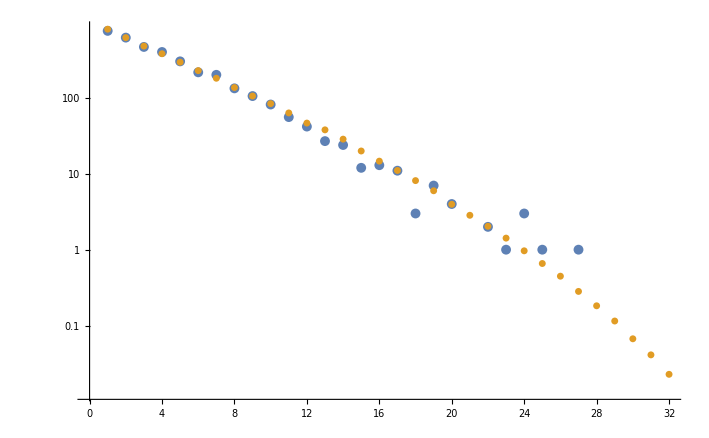

```mathematica
ListLogPlot[{DATA,NevsBCKG+NevsSIGNAL},PlotStyle->{PointSize[0.01],PointSize[0.007]}]
```

```mathematica
DATA
```

{767,625,471,404,304,218,202,134,106,82,56,42,27,24,12,13,11,3,7,4,0,2,1,3,1,0,1,0,0,0,0,0}

```mathematica
Round[NevsBCKG+NevsSIGNAL]
```

{807,625,483,383,297,229,182,137,106,84,64,47,38,29,20,15,11,8,6,4,3,2,1,1,1,0,0,0,0,0,0,0}

## BIG TABLE - ELECTRON

### NOW

```mathematica
totχALL[{C1q1μL_,C3q1μL_,CuRμL_,CuRμR_,Cq1μR_,CdRμL_,CdRμR_,C1q2μL_,C3q2μL_,Cq2μR_,CsRμL_,CsRμR_,CcRμL_,CcRμR_,CbLμL_,CbLμR_,CbRμL_,CbRμR_}]:=Sum[-2 Log[pois[DATA[[bin]],NevsSIGNAL[[bin]]relNevs[(C1q1μL-C3q1μL)/vEW^2,Cq1μR/vEW^2,CuRμL/vEW^2,CuRμR/vEW^2,(C1q1μL+C3q1μL)/vEW^2,Cq1μR/vEW^2,CdRμL/vEW^2,CdRμR/vEW^2,(C1q2μL+C3q2μL)/vEW^2,Cq2μR/vEW^2,CsRμL/vEW^2,CsRμR/vEW^2,(C1q2μL-C3q2μL)/vEW^2,Cq2μR/vEW^2,CcRμL/vEW^2,CcRμR/vEW^2,CbLμL/vEW^2,CbLμR/vEW^2,CbRμL/vEW^2,CbRμR/vEW^2,masa[[bin]]]+ NevsBCKG[[bin]]]],{bin,1,Length[DATA]}];
```

```mathematica
lista=Table[x KroneckerDelta[i,j],{i,18},{j,18}];
lista//MatrixForm
```

(x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x)

```mathematica
For[i=1,i≤18,i++,

rjmin=NMinimize[totχALL[lista[[i]]],x];

Print[ScientificForm[{x/.NMinimize[{(totχALL[lista[[i]]]-rjmin[[1]]-4)^2,x<0},{x}][[2]],x/.NMinimize[{(totχALL[lista[[i]]]-rjmin[[1]]-4)^2,x>0},{x}][[2]]},3]]

]
```

{-1.46×10^-4,1.94×10^-3}

{-8.4×10^-4,4.75×10^-5}

{-3.45×10^-4,2.16×10^-3}

{-5.78×10^-5,2.2×10^-3}

{-5.42×10^-4,1.57×10^-3}

{-2.43×10^-3,1.29×10^-3}

{-2.85×10^-3,7.19×10^-4}

{-7.81×10^-3,5.29×10^-3}

{-9.52×10^-3,2.66×10^-3}

{-5.69×10^-3,7.45×10^-3}

{-8.8×10^-3,7.07×10^-3}

{-9.6×10^-3,6.17×10^-3}

{-1.×10^-2,1.35×10^-2}

{-8.23×10^-3,1.49×10^-2}

{-2.28×10^-2,1.43×10^-2}

{-1.78×10^-2,1.97×10^-2}

{-1.97×10^-2,1.78×10^-2}

{-2.06×10^-2,1.69×10^-2}

```mathematica
rjmin=NMinimize[totχALL[lista[[1]]],x]
```

{159.495,{x→0.00104791}}

```mathematica
totχALL[lista[[1]]]-rjmin[[1]]/.x->{-1.46×10^-4}
totχALL[lista[[1]]]-rjmin[[1]]/.x->{1.94×10^-3}
```

{3.99929}

{3.98805}

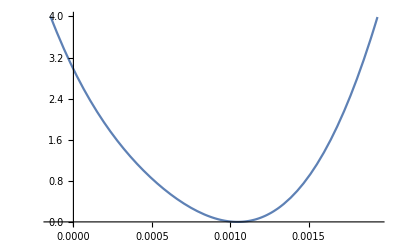

```mathematica
Plot[totχALL[lista[[1]]]-rjmin[[1]],{x,-1.46×10^-4,1.94×10^-3}]
```

### Projections

```mathematica
NexpFUTURE=Round[83.1 (NevsSIGNAL+NevsBCKG)]
```

{67091,51897,40144,31860,24644,19063,15129,11406,8823,7002,5279,3879,3159,2381,1662,1221,921,677,497,330,236,169,118,80,55,37,23,15,10,6,3,2}

```mathematica
totχALL3000[{C1q1μL_,C3q1μL_,CuRμL_,CuRμR_,Cq1μR_,CdRμL_,CdRμR_,C1q2μL_,C3q2μL_,Cq2μR_,CsRμL_,CsRμR_,CcRμL_,CcRμR_,CbLμL_,CbLμR_,CbRμL_,CbRμR_}]:=Sum[-2 Log[pois[NexpFUTURE[[bin]],83.1 NevsSIGNAL[[bin]]relNevs[(C1q1μL-C3q1μL)/vEW^2,Cq1μR/vEW^2,CuRμL/vEW^2,CuRμR/vEW^2,(C1q1μL+C3q1μL)/vEW^2,Cq1μR/vEW^2,CdRμL/vEW^2,CdRμR/vEW^2,(C1q2μL+C3q2μL)/vEW^2,Cq2μR/vEW^2,CsRμL/vEW^2,CsRμR/vEW^2,(C1q2μL-C3q2μL)/vEW^2,Cq2μR/vEW^2,CcRμL/vEW^2,CcRμR/vEW^2,CbLμL/vEW^2,CbLμR/vEW^2,CbRμL/vEW^2,CbRμR/vEW^2,masa[[bin]]]+83.1  NevsBCKG[[bin]]]],{bin,1,Length[bck]}];
```

```mathematica
lista=Table[x KroneckerDelta[i,j],{i,18},{j,18}];
lista//MatrixForm
```

(x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | x)

```mathematica
For[i=1,i≤18,i++,

rjmin=NMinimize[totχALL3000[lista[[i]]],x];

Print[ScientificForm[{x/.NMinimize[{(totχALL3000[lista[[i]]]-rjmin[[1]]-4)^2,x<0},{x}][[2]],x/.NMinimize[{(totχALL3000[lista[[i]]]-rjmin[[1]]-4)^2,x>0},{x}][[2]]},3]]

]
```

Electron future

{-1.1×10^-4,1.24×10^-4}

{-4.37×10^-5,4.32×10^-5}

{-1.68×10^-4,2.03×10^-4}

{-8.88×10^-5,9.26×10^-5}

{-1.95×10^-4,3.05×10^-4}

{-8.28×10^-4,4.57×10^-4}

{-3.81×10^-4,2.89×10^-4}

{-3.6×10^-3,2.09×10^-3}

{-9.69×10^-4,8.59×10^-4}

{-2.35×10^-3,3.57×10^-3}

{-4.31×10^-3,3.02×10^-3}

{-4.2×10^-3,2.34×10^-3}

{-4.02×10^-3,6.27×10^-3}

{-2.86×10^-3,4.7×10^-3}

{-9.4×10^-3,5.24×10^-3}

{-8.04×10^-3,9.63×10^-3}

{-9.62×10^-3,8.08×10^-3}

{-1.02×10^-2,7.23×10^-3}

## Conclusions

```mathematica
Vtb=1;Vts=-0.04159550;
αEM=1/137.04;
vEW=246.22;
δCμ=-0.61;
ΔδCμ=0.12;
```

```mathematica
π/(αEM Vtb Vts)
```

-10350.3

```mathematica
(δCμ αEM Vtb Vts)/π
```

0.0000589358

```mathematica
(vEW/32000)^2
```

0.0000592034

Now

```mathematica
(δCμ αEM Vtb Vts)/π/({-vEW^2/(11326)^2,vEW^2/(7974)^2})
(δCμ αEM Vtb Vts)/π/({-vEW^2/(5784)^2,vEW^2/(7828)^2})
(δCμ αEM Vtb Vts)/π/({-vEW^2/(2253)^2,vEW^2/(2737)^2})
(δCμ αEM Vtb Vts)/π/({-vEW^2/(2216)^2,vEW^2/(1881)^2})
(δCμ αEM Vtb Vts)/π/({-vEW^2/(1469)^2,vEW^2/(1633)^2})
```

{-0.124705,0.0618137}

{-0.0325229,0.0595709}

{-0.00493463,0.00728252}

{-0.00477388,0.00343962}

{-0.00209786,0.00259242}

Future

```mathematica
(δCμ αEM Vtb Vts)/π/{-vEW^2/(28000)^2,vEW^2/(28200)^2}
(δCμ αEM Vtb Vts)/π/{-vEW^2/(18800)^2,vEW^2/(19150)^2}
(δCμ αEM Vtb Vts)/π/{-vEW^2/(5500)^2,vEW^2/(6180)^2}
(δCμ αEM Vtb Vts)/π/{-vEW^2/(4760)^2,vEW^2/(4034)^2}
(δCμ αEM Vtb Vts)/π/{-vEW^2/(2378)^2,vEW^2/(3138)^2}
```

{-0.762164,0.773091}

{-0.343596,0.356508}

{-0.0294075,0.0371287}

{-0.0220265,0.0158199}

{-0.00549738,0.00957278}

## Z’ model

### True limits

```mathematica
2/24+6*1/8
```

5/6

```mathematica
relNevsZmodel[gs_,mV_,Mμμ_]:=relNevs[gs^2/(Mμμ^2-mV^2+I mV (2(mV gs^2)/(24 π)+6 (mV gs^2)/(8 π))),0,0,0,gs^2/(Mμμ^2-mV^2+I mV (2(mV gs^2)/(24 π)+6 (mV gs^2)/(8 π))),0,0,0,gs^2/(Mμμ^2-mV^2+I mV (2(mV gs^2)/(24 π)+6 (mV gs^2)/(8 π))),0,0,0,gs^2/(Mμμ^2-mV^2+I mV (2(mV gs^2)/(24 π)+6 (mV gs^2)/(8 π))),0,0,0,gs^2/(Mμμ^2-mV^2+I mV (2(mV gs^2)/(24 π)+6 (mV gs^2)/(8 π))),0,0,0,Mμμ]
```

```mathematica
relSINGLET[CL_,Mμμ_]:=relNevs[CL,0,0,0,CL,0,0,0,CL,0,0,0,CL,0,0,0,CL,0,0,0,Mμμ];
```

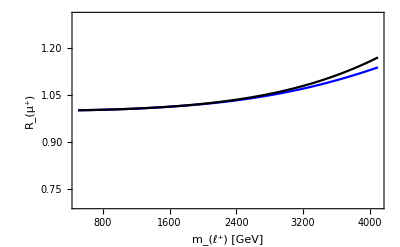

```mathematica
Show[Plot[{relSINGLET[-1/(30000)^2,Mμμ],relNevsZmodel[1/3,10000,Mμμ]},{Mμμ,500,4100},PlotStyle->{Blue,Black,Red},PlotRange->{0.7,1.3},Frame->True,(*GridLines->Automatic,*)FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{{Style["R_(μ^+)", FontSize->20,FontFamily->"Times New Roman",Italic,Black],""},{Style["m_(ℓ^+) [GeV]", FontSize->18,FontFamily->"Times New Roman",Black],Style["dσ (pp → μ^+μ^-) / dσ (pp → e^+e^-) , s_0 = (13 TeV)^2", FontSize->13,FontFamily->"Times New Roman",Bold,Black]}},ImageSize->400]]
```

EFT

```mathematica
totχEFT[CL_]:=Sum[-2 Log[pois[DATA[[bin]],NevsSIGNAL[[bin]]relSINGLET[CL,masa[[bin]]]+ NevsBCKG[[bin]]]],{bin,1,Length[bck]}];
```

```mathematica
rjmin=NMinimize[{totχEFT[x/vEW^2],x<0},{x},Method->"DifferentialEvolution"]
```

{131.199,{x→0.}}

```mathematica
{x/.NMinimize[{(totχEFT[x/vEW^2]-rjmin[[1]]-4)^2,x<0},{x}][[2]],x/.NMinimize[{(totχEFT[x/vEW^2]-rjmin[[1]]-4)^2,x>0},{x}][[2]]}
```

{-0.000685474,0.00145352}

```mathematica
totχEFT[x/vEW^2]-rjmin[[1]]/.{x->-0.000685474}
```

4.

Model

```mathematica
totχMODEL[gs_,mV_]:=Sum[-2 Log[pois[DATA[[bin]],NevsSIGNAL[[bin]]relNevsZmodel[gs,mV,masa[[bin]]]+ NevsBCKG[[bin]]]],{bin,1,Length[bck]}];
```

```mathematica
rjmin=NMinimize[totχMODEL[x,1000],{x},Method->"DifferentialEvolution"]
```

{131.199,{x→-0.00309534}}

```mathematica
lista=Table[{M,(rjmin=NMinimize[totχMODEL[x,M],{x},Method->"DifferentialEvolution"];x/.NMinimize[{(totχMODEL[x,M]-rjmin[[1]]-4)^2,x>0},{x}][[2]])},{M,500,15000,250}]
```

{{500,0.0207635},{750,0.0400619},{1000,0.0417422},{1250,0.0835868},{1500,0.0601717},{1750,0.0951796},{2000,0.111082},{2250,0.0824049},{2500,0.0859683},{2750,0.114868},{3000,0.149992},{3250,0.138798},{3500,0.127697},{3750,0.140392},{4000,0.180444},{4250,0.292777},{4500,0.361813},{4750,0.406822},{5000,0.444976},{5250,0.480003},{5500,0.513268},{5750,0.545417},{6000,0.576815},{6250,0.607689},{6500,0.638194},{6750,0.668444},{7000,0.698526},{7250,0.728511},{7500,0.758462},{7750,0.788432},{8000,0.818473},{8250,0.848633},{8500,0.878959},{8750,0.909501},{9000,0.940308},{9250,0.971435},{9500,1.00294},{9750,1.03488},{10000,1.06733},{10250,1.10036},{10500,1.13406},{10750,1.16854},{11000,1.20389},{11250,1.24026},{11500,1.27781},{11750,1.31672},{12000,1.35721},{12250,1.39958},{12500,1.44416},{12750,1.4914},{13000,1.54189},{13250,1.59642},{13500,1.65608},{13750,1.7225},{14000,1.79817},{14250,1.88734},{14500,1.99817},{14750,2.15036},{15000,3.51259}}

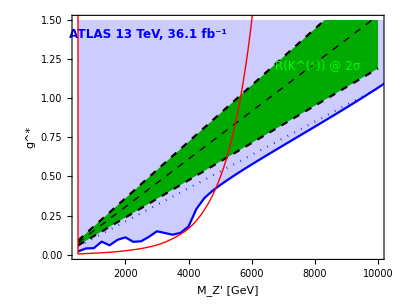

```mathematica
Show[Plot[x √(0.00068547/vEW^2),{x,500,10000},PlotStyle->{{Blue,Dotted}},Frame->True,PlotRange->{{0,10000},{0,1.5}},GridLines->None,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{{Style["g^*", FontSize->20,FontFamily->"Times New Roman",Italic,Black],""},{Style["M_Z' [GeV]", FontSize->18,FontFamily->"Times New Roman",Black],Style["95% CL limits on MFV Z' from p p → μ^+ μ^-", FontSize->13,FontFamily->"Times New Roman",Bold,Black]}},AspectRatio->1/1.3,ImageSize->400],ListPlot[lista,PlotStyle->{Blue},Filling->Top,Joined->True,PlotRange->{{500,10000},{0,1.5}}],Plot[{x/6541,x/8400,x/5541},{x,500,10000},PlotStyle->{{Black,Thin,Dashed},{Black,Dashed},{Black,Dashed}},Frame->True,PlotRange->{{500,10000},{0,1.5}},(*GridLines->Automatic,*)Filling->{2->{3}},FillingStyle->Darker[Green],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{{Style["g^*", FontSize->20,FontFamily->"Times New Roman",Italic,Black],""},{Style["M_Z' [GeV]", FontSize->18,FontFamily->"Times New Roman",Black],Style["95% CL limits on MFV Z' from p p → μ^+ μ^-", FontSize->13,FontFamily->"Times New Roman",Bold,Black]}},ImageSize->400],Graphics[Text[Style["ATLAS 13 TeV, 36.1 fb^-1", FontSize->12,FontFamily->"Times New Roman",Blue,Bold],{2700,1.41}]],Graphics[Text[Style["R(K^(*)) @ 2σ", FontSize->12,FontFamily->"Times New Roman",Green],{8100,1.21}]],ado,PlotRange->{{500,10000},{0,1.5}}]
```

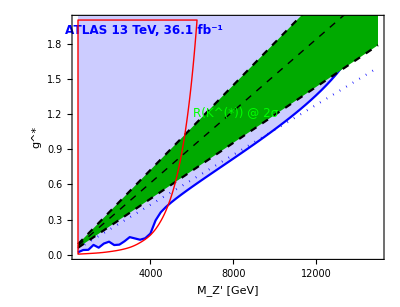

```mathematica
Show[Plot[x √(0.00068547/vEW^2),{x,500,15000},PlotStyle->{{Blue,Dotted}},Frame->True,PlotRange->{{0,15000},{0,√(4π)}},GridLines->None,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{{Style["g^*", FontSize->20,FontFamily->"Times New Roman",Italic,Black],""},{Style["M_Z' [GeV]", FontSize->18,FontFamily->"Times New Roman",Black],Style["95% CL limits on MFV Z' from p p → μ^+ μ^-", FontSize->13,FontFamily->"Times New Roman",Bold,Black]}},AspectRatio->1/1.3,ImageSize->400],ListPlot[lista,PlotStyle->{Blue},Filling->Top,Joined->True,PlotRange->{{500,15000},{0,√(4π)}}],Plot[{x/6541,x/8400,x/5541},{x,500,15000},PlotStyle->{{Black,Thin,Dashed},{Black,Dashed},{Black,Dashed}},Frame->True,PlotRange->{{500,10000},{0,√(4π)}},(*GridLines->Automatic,*)Filling->{2->{3}},FillingStyle->Darker[Green],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[FontSize->15, FontFamily-> "Times New Roman",Black],FrameLabel->{{Style["g^*", FontSize->20,FontFamily->"Times New Roman",Italic,Black],""},{Style["M_Z' [GeV]", FontSize->18,FontFamily->"Times New Roman",Black],Style["95% CL limits on MFV Z' from p p → μ^+ μ^-", FontSize->13,FontFamily->"Times New Roman",Bold,Black]}},ImageSize->400],Graphics[Text[Style["ATLAS 13 TeV, 36.1 fb^-1", FontSize->12,FontFamily->"Times New Roman",Blue,Bold],{3700,1.91}]],Graphics[Text[Style["R(K^(*)) @ 2σ", FontSize->12,FontFamily->"Times New Roman",Green],{8100,1.21}]],ado,PlotRange->{{500,15000},{0,2}}]
```

```mathematica
(5 2.0^2)/(6π)
```

1.06103

### Wrong limits

BR = 1/24:5/6

σ × BR < Something

```mathematica
(1/24)/(5/6)
```

1/20

```mathematica
σVp={{500,2013},{1000,143.6},{1500,24.6},{2000,5.865},{2500,1.657},{3000,0.5166},{3500,0.1692},{4000,0.05699},{4500,0.01948},{5000,0.006583},{5500,0.002192},{6000,0.0007161},{6500,0.0002234}}
```

{{500,2013},{1000,143.6},{1500,24.6},{2000,5.865},{2500,1.657},{3000,0.5166},{3500,0.1692},{4000,0.05699},{4500,0.01948},{5000,0.006583},{5500,0.002192},{6000,0.0007161},{6500,0.0002234}}

```mathematica
logσVp=Table[{σVp[[i,1]],Log[σVp[[i,2]]]},{i,1,Length[σVp]}];
flogσVp=Interpolation[logσVp];
fσVp[mV_]:=Exp[flogσVp[mV]];
funkσVp[mV_,κq_]:=fσVp[mV] κq^2;
kappaq[σ_,mV_]:=Sqrt[σ/fσVp[mV]];
```

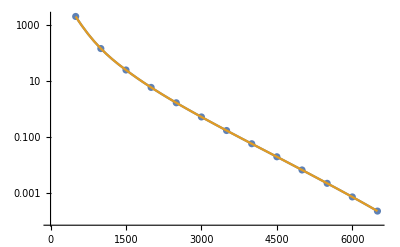

```mathematica
ado=ListLogPlot[σVp];
alma=LogPlot[{fσVp[x],funkσVp[x,1]},{x,500,6500}];
Show[ado,alma]
```

```mathematica
limits={{500,25*10^-4},{1000,7*10^-4},{1500,3*10^-4},{2000,1.9*10^-4},{2500,1.3*10^-4},{3000,1*10^-4},{3500,0.9*10^-4},{4000,0.8*10^-4},{4500,0.8*10^-4},{5000,0.8*10^-4},{5500,0.8*10^-4},{6000,0.8*10^-4},{6500,0.8*10^-4}}
```

{{500,1/400},{1000,7/10000},{1500,3/10000},{2000,0.00019},{2500,0.00013},{3000,1/10000},{3500,0.00009},{4000,0.00008},{4500,0.00008},{5000,0.00008},{5500,0.00008},{6000,0.00008},{6500,0.00008}}

```mathematica
logσVpLIMIT=Table[{limits[[i,1]],Log[limits[[i,2]]]},{i,1,Length[limits]}];
flogσVpLIMIT=Interpolation[logσVpLIMIT];
fσVpLIMIT[mV_]:=Exp[flogσVpLIMIT[mV]];
```

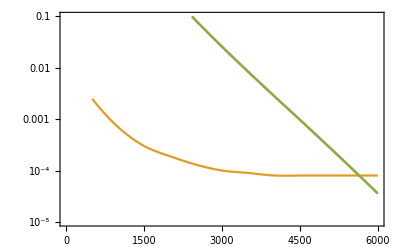

```mathematica
LogPlot[{fσVp[x] 1/20,fσVpLIMIT[x],funkσVp[x,1] 1/20},{x,500,6000},PlotRange->{10^-5,10^-1},Frame->True]
```

```mathematica
funkσVp[500,0.1] 6/(24 5)
```

1.0065

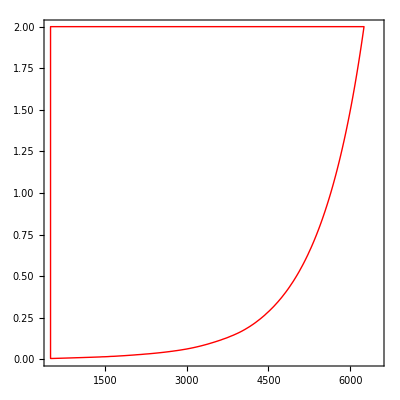

```mathematica
ado=RegionPlot[funkσVp[x,y] 1/20> fσVpLIMIT[x],{x,500,6500},{y,0,2},PlotStyle->{None},BoundaryStyle->{Red,Thin}]
```